```mathematica
(* Taboo Transition of the last transition step *)
```

```mathematica
f[y_]:=(1-Exp[-2n(g2-y)(g1-x)])PDF[NormalDistribution[0,1/(√n)],y-x]If[y<g2,1,0]
```

```mathematica
(*Fourier transform of the transition step*)
```

```mathematica
Assuming[n>0 &&g1>0 &&g2>0 && Element[g1, Reals] && Element[g2, Reals]&& Element[x, Reals]&& Element[y, Reals] && Element[n, Reals],FourierTransform[f[t],t,s,FourierParameters->{0,-2Pi}]]
```

```mathematica
fhat[s_]:=(ⅇ^(-(2 π s (π s+ⅈ n x))/n-2 g1 (g2 n+2 ⅈ π s+n x)) √n (ⅇ^(2 g1 (g2 n+2 ⅈ π s+n x)) (g2 n+2 ⅈ π s-n x) √((-2 g1 n+g2 n+2 ⅈ π s+n x)^2) Erf[(√((g2 n+2 ⅈ π s-n x)^2/n))/(√2)]+√((g2 n+2 ⅈ π s-n x)^2) ((ⅇ^(2 g1 (g2 n+2 ⅈ π s+n x))-ⅇ^(2 g1^2 n+2 g2 n x+4 ⅈ π s x)) √((-2 g1 n+g2 n+2 ⅈ π s+n x)^2)+ⅇ^(2 g1^2 n+2 g2 n x+4 ⅈ π s x) (2 g1 n-g2 n-2 ⅈ π s-n x) Erf[(√((-2 g1 n+g2 n+2 ⅈ π s+n x)^2/n))/(√2)])))/(2 √(n (g2 n+2 ⅈ π s-n x)^2) √((-2 g1 n+g2 n+2 ⅈ π s+n x)^2))
```

```mathematica
(* Simplified version of the transition FT, with parameter s*)
```

```mathematica
FullSimplify[fhat[s],n>0 &&g1>0 &&g2>0 && Element[g1, Reals] && Element[g2, Reals]&& Element[x, Reals]&& Element[s, Reals] && Element[n, Reals]]
```

1/2 ⅇ^(-(2 π s (π s+ⅈ n x))/n) (1+Erf[(g2 n+2 ⅈ π s-n x)/(√2 √n)]+ⅇ^(2 (g1 n-g2 n-2 ⅈ π s) (g1-x)) (-2+Erfc[(2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))

```mathematica
(*Simplified Fourier transform*)
```

```mathematica
fhatsimp[s_]:=1/2 ⅇ^(-(2 π s (π s+ⅈ n x))/n) (1+Erf[(g2 n+2 ⅈ π s-n x)/(√2 √n)]+ⅇ^(2 (g1 n-g2 n-2 ⅈ π s) (g1-x)) (-2+Erfc[(2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))
```

```mathematica
(* Seems like the absolute value decays to zero. *)
```

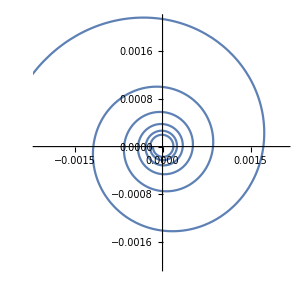

```mathematica
ParametricPlot[{Re[fhatsimp[s]]/. n -> 3 /. g1-> 1 /.x-> 0.9 /. g2-> 1,Im[fhatsimp[s]]/. n -> 3 /. g1-> 1 /.x-> 0.9 /. g2-> 1},{s,1,8}]
```

```mathematica
(* zooming out to tails slows this down dramatically*)
```

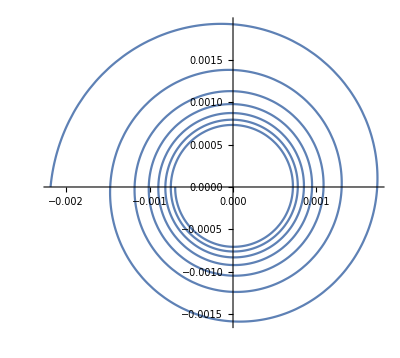

```mathematica
ParametricPlot[{Re[fhatsimp[n]] /. g1-> 1 /.x-> 0.9 /. g2-> 1,Im[fhatsimp[n]] /. g1-> 1 /.x-> 0.9 /. g2-> 1},{n,1,8}]
```

```mathematica
(* we get that absolute value also decays like 1/s^2 for fixed n*)
```

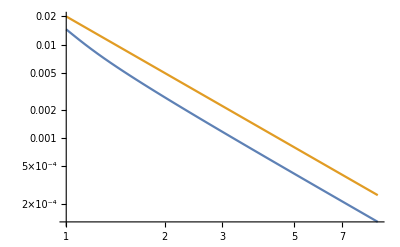

```mathematica
LogLogPlot[{Abs[fhatsimp[s]]/. n -> 3 /. g1-> 1 /.x-> 0.9 /. g2-> 1,0.02/s^2},{s,1,9}]
```

```mathematica
Manipulate[{ⅇ^(2 n(g1 -g2)(g1-x))ⅇ^(-4ⅈ π s(g1-x))Erfc[(2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]/.s->n ,
Erfc[(g2 n+2 ⅈ π s-n x)/(√2 √n)]/.s->n,
ⅇ^(2 n(g1 -g2 )(g1-x))ⅇ^(-4ⅈ π s(g1-x))Erfc[(2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)] - Erfc[(g2 n+2 ⅈ π s-n x)/(√2 √n)]/.s->n}//MatrixForm,{n,1,10},{ g1, 0.5,1},{x,-3,g1},{ g2,0.5,1} ]
```

```mathematica
(* green is the subtracted *)
```

```mathematica
Manipulate[ParametricPlot[{{t,t Im[ⅇ^(2 n(g1 -g2)(g1-x))ⅇ^(-4ⅈ π s(g1-x))Erfc[(2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]]/Re[ⅇ^(2 n(g1 -g2)(g1-x))ⅇ^(-4ⅈ π s(g1-x))Erfc[(2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]]/.s->n },{t,t Im[Erfc[(g2 n+2 ⅈ π s-n x)/(√2 √n)]]/Re[Erfc[(g2 n+2 ⅈ π s-n x)/(√2 √n)]]/.s->n},
{t,t Im[ⅇ^(2 n(g1 -g2 )(g1-x))ⅇ^(-4ⅈ π s(g1-x))Erfc[(2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)] - Erfc[(g2 n+2 ⅈ π s-n x)/(√2 √n)]]/Re[ⅇ^(2 n(g1 -g2 )(g1-x))ⅇ^(-4ⅈ π s(g1-x))Erfc[(2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)] - Erfc[(g2 n+2 ⅈ π s-n x)/(√2 √n)]]/.s->n }},{t,0,1},PlotRange->{{-1,1},{-1,1}}],{ g1, 0.5,1},{x,-3,g1},{ g2,0.5,1 - 2/n} ,{n,1,30,1}]
```

```mathematica
`
```

```mathematica
(* The crude triangle inequality works when g1 is far from x. But as x -> g, the difference between the two erfc should decay to 0*)
```

```mathematica
Manipulate[{Abs[ⅇ^(2 n(g1 -g2)(g1-x))ⅇ^(-4ⅈ π s(g1-x))Erfc[(2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]]/.s->n ,
Abs[Erfc[(g2 n+2 ⅈ π s-n x)/(√2 √n)]]/.s->n,
Abs[ⅇ^(2 n(g1 -g2 )(g1-x))ⅇ^(-4ⅈ π s(g1-x))Erfc[(2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)] - Erfc[(g2 n+2 ⅈ π s-n x)/(√2 √n)]]/.s->n,
Abs[ⅇ^(2 n(g1 -g2 )(g1-x))ⅇ^(-4ⅈ π s(g1-x))Erfc[(2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)] ]+Abs[ Erfc[(g2 n+2 ⅈ π s-n x)/(√2 √n)]]/.s-> n}//MatrixForm,{n,1,10},{ g1, 0.5,1},{x,0,g1},{ g2,0.5,1} ]
```

```mathematica
fhatsimp[s_]:=1/2 ⅇ^(-(2 π s (π s+ⅈ n x))/n) (1+Erf[(g2 n+2 ⅈ π s-n x)/(√2 √n)]+ⅇ^(2 (g1 n-g2 n-2 ⅈ π s) (g1-x)) (-2+Erfc[(2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))
```

```mathematica
(* The convergence rate should be dependent on (g1 - x1). Error rate is not taken into account when x1 near -∞. *)
```

```mathematica
Manipulate[LogLogPlot[{Abs[fhatsimp[s n^α]] /. g1-> g/.x-> x1 /. g2-> g+Kc/n,
Abs[4 √(2/π)(n^(3/2)(g1 -x)ⅇ^(-n/2(g2 -x)^2))/(n^2(g1-x)^2+(2π s n^α)^2)]+ⅇ^(-2/n π^2(s n^α)^2)/.x-> x1 /. g1->g/.g2->g+Kc/n,
Abs[4 √(2/π)(n^(3/2)(g1 -x)ⅇ^(-n/2(g2 -x)^2))/((2π s n^α)^2)]+ⅇ^(-2/n π^2(s n^α)^2)/.x-> x1 /. g1->g/.g2->g+Kc/n,
n^(-2α)2n BernoulliB[2]/(2!)(g1-x)PDF[NormalDistribution[0,1/(√n)],g2-x]/.x-> x1 /. g1->g/.g2->g+Kc/n,
1/n^2},
{n,1,10^2},PlotRange->Automatic,PlotStyle->{Opacity[a],Opacity[b],Opacity[c],Opacity[d],Dashed},PlotLegends ->{"Abs error","PSF","PSF2","EMSF","1/m^2"}],
{{x1,0},-12,g},
{s,1,3,1},
{{Kc,0},-3,3},
{{α,1},0.5,1.5},
{{g,0.5},0.5,2.5},
{{a,1,"ABS"},{1,0}},
{{b,1,"PSF"},{1,0}},
{{c,1,"PSF v2"},{1,0}},
{{d,1,"EMSF"},{1,0}},
ControlPlacement->Left]
```

```mathematica
Manipulate[LogLogPlot[{Abs[fhatsimp[s n^α]]/(Abs[4 √(2/π)(n^(3/2)(g1 -x)ⅇ^(-n/2(g2 -x)^2))/((2π s n^α)^2)]+ⅇ^(-2/n π^2(s n^α)^2))/. g1-> g/.x-> x1 /. g2-> g+Kc/n,
Abs[fhatsimp[s n^α]]/(n^(-2α)2n BernoulliB[2]/(2!)(g1-x)PDF[NormalDistribution[0,1/(√n)],g2-x])/.x-> x1 /. g1->g/.g2->g+Kc/n},
{n,1,10^4},PlotRange->Automatic,PlotStyle->{Opacity[a],Opacity[b]},PlotLegends ->{"Abs error","EMSF"}],
{{x1,0},-12,g},
{s,1,3,1},
{{Kc,0},-3,3},
{{α,1},0.5,1.5},
{{g,0.5},0.5,2.5},
{{a,1,"ABS"},{1,0}},
{{b,1,"EMSF"},{1,0}},
ControlPlacement->Left]
```

```mathematica
Limit[Erfc[z],z->ⅈ ∞]
```

(-ⅈ) ∞

```mathematica
Erfc[10ⅈ]//N
```

-9.33369×10^25-1.52431×10^42 ⅈ

```mathematica
Abs[fhatsimp[500]]/.n-> 500/. g1-> 0.5 /.x->-2.17 /. g2-> 0.5//N
```

1.99560099607621×10^-777

```mathematica
,PlotStyle->{Opacity[a],Opacity[b],Opacity[c],Opacity[d],Opacity[e]},PlotLegends ->{"Abs error","EMSF","Vincent","Vincent v2","1/n^4"}],
{x0s,-3,1-0.01},
{x2s,-3,1-0.01},
{s,1,10,1},
{{Kc,0},-3,3},
{{α,1},0.5,1.5},
{{a,1,"ABS"},{1,0}},
{{b,1,"EMSF"},{1,0}},
{{c,1,"v1"},{1,0}},
{{d,1,"v2"},{1,0}},
{{e,1,"1/n^4"},{1,0}},
ControlPlacement->Left
```

```mathematica
(* Our asymptotic expansion works!*)
```

```mathematica
Manipulate[LogLogPlot[{Abs[fhatsimp[s m^α]] /. g1-> 1 /.x-> x1 /. g2-> 1+K/n,
Abs[√(2/(n π))((g1 -x)ⅇ^(-n/2(g2 -x)^2))/(√((-2 g1 g2+g2^2-4 π^2 (s m^α)^2+2 g1 x-x^2)^2+(-4 π g1 s m^α +4 π g2 s m^α)^2))]/.x-> x1 /. g1->1/.g2-> 1+K/n,
Abs[√(2/π)(n^(3/2)(g1 -x)ⅇ^(-n/2(g2 -x)^2))/Abs[n^2(g2 - g1)^2-n^2(g1-x)^2-(2π s m^α)^2]]/.x-> x1 /. g1->1/.g2-> 1+K/n,
1/n^2},
{n,1,10^3},PlotStyle->{Blue,Red,Green,Dashed},PlotLegends ->{"Abs error","Vincent","Vincent V2","1/m^2"},PlotRange->{{1,10^2},{10^-12,1}}],{m,1,100,1},{x1,
-3,1-0.01},{α,0.5,1},{s,1,10,1},{K,-3,3}]
```

K$$::shdw: Symbol K$$ appears in multiple contexts {System`,Global`}; definitions in context System` may shadow or be shadowed by other definitions.

```mathematica
(* Real part and abs part is the same stuff*)
```

```mathematica
Manipulate[LogLogPlot[{Abs[Re[fhatsimp[n]]] /. g1-> 1 /.x-> x1 /. g2-> 1,Abs[√(2/(n π))((g1 -x)ⅇ^(-n/2(g2 -x)^2))/(√((-2 g1 g2+g2^2-4 π^2 s^2+2 g1 x-x^2)^2+(-4 π g1 s +4 π g2 s)^2))]/.s->1/.x-> x1 /. g1->1/.g2-> 1,1/n^2,1/(√n)},{n,10,1000},PlotStyle->{Blue,Red,Dashed,Dashed},PlotLegends ->{"Abs error","Vincent","1/n^2", "1/√n"}],{x1,
0.7,1-0.01}]
```

```mathematica
(* It is clear that the first term in the sum is the dominant term*)
```

```mathematica
Manipulate[LogLogPlot[{Abs[fhatsimp[√n]]/. g1-> 1 /.x-> x1 /. g2-> 1,∑_(k=1)^20 Abs[fhatsimp[k √n]] /. g1-> 1 /.x-> x1 /. g2-> 1,1/n^2,1/(√n)},{n,1,90},PlotStyle->{Blue,Orange,Green, Dashed,Dashed},PlotLegends ->{"First point Abs error","Abs error","1/n^2", "1/√n"}],{x1,-3,1-0.01}]
```

```mathematica
(* (n(g-x)+2 ⅈ π k n)/(√2 √n) becomes √(n/2)((g-x) + 2 π k i). Since (g-x) is positive, we will be in the posiitve real half plane. So is 2πk. Hence we will be in the upper right sector of the complex plane.*)
(* From *)
```

```mathematica
(*Expressed erfs in terms of CDFs, from DLMF there is an asymptotic expansion 
Erfc[z] ~ Exp[-z^2]/(√π)∑_(m=0)^∞ (-1)^m/z^(2m+1)Subscript[(1/2), m]   valid for arg(z) < (3π)/4 , with different error terms when |arg(z)| < π/4 and |arg(z)| ϵ [π/4,π/2)*)
Series[Erfc[z],{z,∞,3}]
```

ⅇ^(-z^2) (1/(√π z)-1/(2 √π z^3)+O[1/z]^4)

```mathematica
√(2/(n π))((g1 -x)ⅇ^(-n/2(g2 -x)^2))/(√((-2 g1 g2+g2^2-4 π^2 s^2+2 g1 x-x^2)^2+(-4 π g1 s +4 π g2 s)^2)) /. g2->g1/.g1->1 /. s-> 1
```

(ⅇ^(-1/2 n (1-x)^2) √(1/n) √(2/π) (1-x))/(√((-1-4 π^2+2 x-x^2)^2))

```mathematica
(* Finally, the elusive h^2*)
```

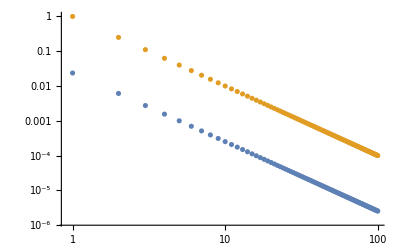

```mathematica
ListLogLogPlot[{Table[√(2/(n π))NIntegrate[(1 - x)^2(ⅇ^(-1/2 n (1-x)^2))/(√((-1-4 π^2+2 x-x^2)^2)),{x,-∞,1}] //N,{n,1,100}],Table[1/n^2,{n,1,100}]}]
```

```mathematica
(*For the middle terms*)
```

```mathematica
f2[x1_]:=(1-Exp[-2n(g2-x2)(g1-x1)])PDF[NormalDistribution[0,1/(√n)],x2-x1](1-Exp[-2n(g0-x0)(g1-x1)])PDF[NormalDistribution[0,1/(√n)],x1-x0]If[x1<g1,1,0]
```

```mathematica
Assuming[n>0 &&g0>0&&g1>0 && g2>0 && Element[g0, Reals]&& Element[g1, Reals] && Element[g2, Reals]&& Element[x2, Reals]&& Element[x1, Reals]&& Element[x0, Reals] && Element[n, Reals],FourierTransform[f2[t],t,s,FourierParameters->{0,-2Pi}]]
```

(ⅇ^(-2 ⅈ g0 π s-2 ⅈ g2 π s-(π^2 s^2)/n-g0 n x0-g2 n x0-ⅈ π s x0+(n x0^2)/4-g0 n x2-g2 n x2-ⅈ π s x2-(n x0 x2)/2+(n x2^2)/4-1/2 n (4 g0 g1+4 g1 g2+x0^2+x2^2)) (-ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) n √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2)-ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) n √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2)+ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) n √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2)+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) n √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2)+2 ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) g0 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) g1 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-2 ⅈ ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) n π s √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) n^2 x0 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) n^2 x2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-2 ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) g1 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]+2 ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) g2 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-2 ⅈ ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) n π s √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]+ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) n^2 x0 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) n^2 x2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) g0 n √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) g1 n √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) g2 n √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅈ ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) π s √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) n x0 √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) n x2 √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) g1 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]+2 ⅈ ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) n π s √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]-ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) n^2 x0 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]-ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) n^2 x2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]))/(4 √n √π √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))

```mathematica
f2hat[s_]:=(ⅇ^(-2 ⅈ g0 π s-2 ⅈ g2 π s-(π^2 s^2)/n-g0 n x0-g2 n x0-ⅈ π s x0+(n x0^2)/4-g0 n x2-g2 n x2-ⅈ π s x2-(n x0 x2)/2+(n x2^2)/4-1/2 n (4 g0 g1+4 g1 g2+x0^2+x2^2)) (-ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) n √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2)-ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) n √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2)+ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) n √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2)+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) n √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2)+2 ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) g0 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) g1 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-2 ⅈ ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) n π s √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) n^2 x0 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) n^2 x2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-2 ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) g1 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]+2 ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) g2 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-2 ⅈ ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) n π s √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]+ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) n^2 x0 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) n^2 x2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) g0 n √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) g1 n √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) g2 n √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅈ ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) π s √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) n x0 √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) n x2 √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) g1 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]+2 ⅈ ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) n π s √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]-ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) n^2 x0 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]-ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) n^2 x2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]))/(4 √n √π √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))
```

```mathematica
Simplify[f2hat[s],n>0 &&g0>0&&g1>0 && g2>0 && Element[s,Reals]&&Element[g0, Reals]&& Element[g1, Reals] && Element[g2, Reals]&& Element[x2, Reals]&& Element[x1, Reals]&& Element[x0, Reals] && Element[n, Reals]]
```

1/(4 √π)ⅇ^(-(π^2 s^2)/n-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) ((ⅇ^(g0^2 n-2 g0 g1 n-2 ⅈ g0 π s-g0 n x0+2 g1 n x0+2 ⅈ π s x0+g0 n x2) √(n (-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2) Erf[1/2 √((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2/n)])/(2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)+√n ((ⅇ^(g2^2 n+2 ⅈ π s x2+2 g1 n (-g2+x2)+g2 (-2 ⅈ π s+n x0-n x2)) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[1/2 √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2/n)])/(-2 g1 n+2 g2 n-2 ⅈ π s+n x0-n x2)+(ⅇ^(-g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)-g2 (2 ⅈ π s+n (x0+x2))) (ⅇ^(g0^2 n+g2^2 n+2 ⅈ π s x0+g0 (2 g1 n+2 ⅈ π s+n x0)+2 ⅈ π s x2+n x0 x2+2 g1 n (-g2+x0+x2)) (-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2) Erf[1/2 √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/n)]+ⅇ^(-2 g1 g2 n) √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) (ⅇ^(g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0)) (-ⅇ^(g0^2 n+2 ⅈ g2 π s+g2 n x0+2 ⅈ π s x0+2 g1 n (g2+x0)+2 g0 n x2+g2 n x2)+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2)-ⅇ^(g2^2 n+2 g2 n x0+2 g1 n x2+2 ⅈ π s x2+g0 (2 g1 n+2 ⅈ π s+n (x0+x2)))+ⅇ^(2 g1 g2 n+2 ⅈ g2 π s+g2 n x0+g2 n x2+n x0 x2+g0 (2 g1 n+2 ⅈ π s+n (x0+x2)))) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2)+ⅇ^(2 g1 g2 n+2 ⅈ g2 π s+g2 n x0+g2 n x2+n x0 x2+g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)) (2 g1 n+2 ⅈ π s-n (x0+x2)) Erf[1/2 √((2 g1 n+2 ⅈ π s-n (x0+x2))^2/n)])))/(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2))))

```mathematica
fh4hatsimp[s_]:=1/(4 √π)ⅇ^(-(π^2 s^2)/n-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) ((ⅇ^(g0^2 n-2 g0 g1 n-2 ⅈ g0 π s-g0 n x0+2 g1 n x0+2 ⅈ π s x0+g0 n x2) √(n (-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2) Erf[1/2 √((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2/n)])/(2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)+√n ((ⅇ^(g2^2 n+2 ⅈ π s x2+2 g1 n (-g2+x2)+g2 (-2 ⅈ π s+n x0-n x2)) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[1/2 √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2/n)])/(-2 g1 n+2 g2 n-2 ⅈ π s+n x0-n x2)+(ⅇ^(-g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)-g2 (2 ⅈ π s+n (x0+x2))) (ⅇ^(g0^2 n+g2^2 n+2 ⅈ π s x0+g0 (2 g1 n+2 ⅈ π s+n x0)+2 ⅈ π s x2+n x0 x2+2 g1 n (-g2+x0+x2)) (-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2) Erf[1/2 √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/n)]+ⅇ^(-2 g1 g2 n) √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) (ⅇ^(g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0)) (-ⅇ^(g0^2 n+2 ⅈ g2 π s+g2 n x0+2 ⅈ π s x0+2 g1 n (g2+x0)+2 g0 n x2+g2 n x2)+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2)-ⅇ^(g2^2 n+2 g2 n x0+2 g1 n x2+2 ⅈ π s x2+g0 (2 g1 n+2 ⅈ π s+n (x0+x2)))+ⅇ^(2 g1 g2 n+2 ⅈ g2 π s+g2 n x0+g2 n x2+n x0 x2+g0 (2 g1 n+2 ⅈ π s+n (x0+x2)))) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2)+ⅇ^(2 g1 g2 n+2 ⅈ g2 π s+g2 n x0+g2 n x2+n x0 x2+g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)) (2 g1 n+2 ⅈ π s-n (x0+x2)) Erf[1/2 √((2 g1 n+2 ⅈ π s-n (x0+x2))^2/n)])))/(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2))))
```

```mathematica
vincancel[s_]:=1/(2 π)ⅇ^(-g1^2 n-1/2 n (x0^2+x2^2)+g1 (-2 ⅈ π s+n (x0+x2))) n (1/(-2 ⅈ π s+n (-2 g1+2 g2+x0-x2))+1/(-2 ⅈ π s+n (2 g0-2 g1-x0+x2))+√n ((√((-2 ⅈ π s+n (-2 g1+x0+x2))^2) √((-2 ⅈ π s+n (-2 g1+x0+x2))^2/n))/(2 g1 n+2 ⅈ π s-n (x0+x2))^3-(√((2 ⅈ π s+n (-2 g0+2 g1-2 g2+x0+x2))^2) √((2 ⅈ π s+n (-2 g0+2 g1-2 g2+x0+x2))^2/n))/(2 g0 n-2 ⅈ π s-n (2 g1-2 g2+x0+x2))^3))
```

```mathematica
(*Symmetric in the imaginary*)
```

```mathematica
Abs[fh4hatsimp[-30]]/. g0 -> 1/. g1-> 1 /. g2-> 1/.x0->0.5/.x2->0.5 /. n-> 10//N
```

3.9035×10^-6

```mathematica
N[Re[fh4hatsimp[5]],100]/. g0 -> 1/. g1-> 1 /. g2-> 1.1/.x0->0.5/.x2->0.5 /. n-> 10
```

-0.0000949355

```mathematica
fh4hatsimp[30]/. g0 -> 1/. g1-> 1 /. g2-> 1/.x0->0/.x2->0 /. n-> 10//N
```

0.-8.56339×10^-9 ⅈ

```mathematica
fh4hatsimp[π]/. g0 -> 1/. g1-> 1 /. g2-> 1/.x0->0/.x2->0 /. n-> 10//N
```

0.0000491601-2.68572×10^-6 ⅈ

```mathematica
Abs[f2hat[n]]/. n -> 3 /.g0->1/. g1-> 1/.g2 ->1 /.x0-> 0.9/.x2-> 0.9
```

0.0000555577

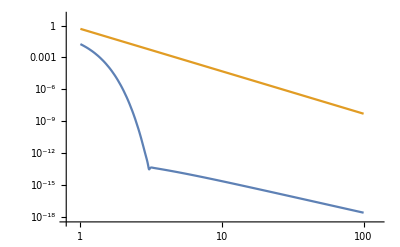

```mathematica
LogLogPlot[{Abs[f2hat[s]]/. n -> 3 /.g0->1/. g1-> 1/.g2 ->1 /.x0-> -2/.x2-> -2,0.5/s^4 },{s,1,100}]
```

```mathematica
(* Low x0 and x2 values make the error not match up with EMSF. But this happened in h2 as well. *)
```

```mathematica
Manipulate[LogLogPlot[{
Abs[f2hat[s n^α]] /. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,
48 n n^(-4 α)/(30 (4!))(g2-x2)(g0-x0)PDF[NormalDistribution[0,1/(√n)],g1 - x2]PDF[NormalDistribution[0,1/(√n)],g1 - x0]/. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,
Abs[vincancel[s n^α]] /. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,
Abs[vincentcancel2[s n^α ]]/. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,
1/n^4},
{n,1,10},PlotStyle->{Blue,Red,Green,Purple,Dashed},PlotLegends ->{"Abs error","EMSF","Vincent","Vincent2","1/n^4"}],
{x0s,-3,1-0.01},
{x2s,-3,1-0.01},
{s,1,10,1},
{Kc,-3,3},
{α,0.5,1.5}]
```

```mathematica
Manipulate[LogLogPlot[{
Abs[f2hat[s n^α]] /. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,
48 n n^(-4 α)/(30 (4!))(g2-x2)(g0-x0)PDF[NormalDistribution[0,1/(√n)],g1 - x2]PDF[NormalDistribution[0,1/(√n)],g1 - x0]/. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,
Abs[vinv2[s n^α]]  /. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,
1/n^4},
{n,1,10},PlotStyle->{Opacity[a],Opacity[b],Opacity[c],Opacity[d]},PlotLegends ->{"Abs error","EMSF","Vincent","1/n^4"}],
{x0s,-3,1},
{x2s,-3,1},
{s,1,10,1},
{{Kc,0},-3,3},
{{α,1},0.5,1.5},
{{a,1,"ABS"},{1,0}},
{{b,1,"EMSF"},{1,0}},
{{c,1,"v1"},{1,0}},
{{d,1,"1/n^4"},{1,0}},
ControlPlacement->Left]
```

```mathematica
Manipulate[LogLogPlot[{
Abs[fh4hatsimp[s n^α]] /. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,
48 n n^(4 α)/(30 (4!))(g2-x2)(g0-x0)PDF[NormalDistribution[0,1/(√n)],g1 - x2]PDF[NormalDistribution[0,1/(√n)],g1 - x0]/. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,
Abs[vincancel[s n^α]] /. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,
Abs[vincentcancel2[s n^α ]]/. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,
1/n^4},
{n,1,10},PlotStyle->{Blue,Red,Green,Purple,Dashed},PlotLegends ->{"Abs error","EMSF","Vincent","Vincent2","1/n^4"}],
{x0s,-3,1-0.01},
{x2s,-3,1-0.01},
{s,1,10,1},
{Kc,-3,3},
{α,0.5,1.5}]
```

```mathematica
Im[fh4hatsimp[0.4]]/. n -> 3/. g0->0 /. g1-> 1 /.x0-> 0.9 /. x2 -> 0.8 /. g2-> 1
```

-1.85543

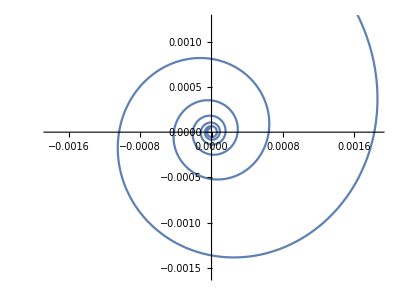

```mathematica
ParametricPlot[{N[Re[fh4hatsimp[s]]]/. n -> 3 /. g0->0/.g1-> 1 /.x0-> 0.9 /. x2 -> 0.8 /. g2-> 1,N[Im[fh4hatsimp[s]]]/. n -> 3/. g0->0 /. g1-> 1 /.x0-> 0.9 /. x2 -> 0.8 /. g2-> 1},{s,1,8}]
```

```mathematica
FullSimplify[fh4hatsimp[s],n>0 &&g0>0&&g1>0 &&g2>0 &&g1>x1&& Element[g0, Reals]&& Element[g1, Reals] && Element[g2, Reals]&& Element[x0, Reals]&& Element[x1, Reals]&& Element[x2, Reals]&& Element[s, Reals] && Element[n, Integers]]
```

$Aborted

```mathematica
z1 = 1/2 √((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2/n)
```

1/2 √((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2/n)

```mathematica
z2=1/2 √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2/n)
```

1/2 √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2/n)

```mathematica
z3=1/2 √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/n)
```

1/2 √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/n)

```mathematica
z4 = 1/2 √((2 g1 n+2 ⅈ π s-n (x0+x2))^2/n)
```

1/2 √((2 g1 n+2 ⅈ π s-n (x0+x2))^2/n)

```mathematica
Series[Erf[z],{z,∞,1}]
```

1+ⅇ^(-z^2) (-1/(√π z)+O[1/z]^2)

```mathematica
aprox[z_]:=(ⅇ^(-z^2))/(√π z)
```

```mathematica
Erf[10+10ⅈ]//N
```

0.961649-0.0109877 ⅈ

```mathematica
aprox[10+10ⅈ] //N
```

0.961621-0.010892 ⅈ

```mathematica
Erfc[10+10ⅈ]//N
```

0.0383506+0.0109877 ⅈ

```mathematica
(*Replace all the erfc*)
```

```mathematica
1/(4 √π)ⅇ^(-(π^2 s^2)/n-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) ((ⅇ^(g0^2 n-2 g0 g1 n-2 ⅈ g0 π s-g0 n x0+2 g1 n x0+2 ⅈ π s x0+g0 n x2) √(n (-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2) (1-Erfc[1/2 √((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2/n)]))/(2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)+√n ((ⅇ^(g2^2 n+2 ⅈ π s x2+2 g1 n (-g2+x2)+g2 (-2 ⅈ π s+n x0-n x2)) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2)(1- Erfc[1/2 √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2/n)]))/(-2 g1 n+2 g2 n-2 ⅈ π s+n x0-n x2)+(ⅇ^(-g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)-g2 (2 ⅈ π s+n (x0+x2))) (ⅇ^(g0^2 n+g2^2 n+2 ⅈ π s x0+g0 (2 g1 n+2 ⅈ π s+n x0)+2 ⅈ π s x2+n x0 x2+2 g1 n (-g2+x0+x2)) (-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2) (1-Erfc[1/2 √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/n)])+ⅇ^(-2 g1 g2 n) √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) (ⅇ^(g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0)) (-ⅇ^(g0^2 n+2 ⅈ g2 π s+g2 n x0+2 ⅈ π s x0+2 g1 n (g2+x0)+2 g0 n x2+g2 n x2)+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2)-ⅇ^(g2^2 n+2 g2 n x0+2 g1 n x2+2 ⅈ π s x2+g0 (2 g1 n+2 ⅈ π s+n (x0+x2)))+ⅇ^(2 g1 g2 n+2 ⅈ g2 π s+g2 n x0+g2 n x2+n x0 x2+g0 (2 g1 n+2 ⅈ π s+n (x0+x2)))) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2)+ⅇ^(2 g1 g2 n+2 ⅈ g2 π s+g2 n x0+g2 n x2+n x0 x2+g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)) (2 g1 n+2 ⅈ π s-n (x0+x2)) (1-Erfc[1/2 √((2 g1 n+2 ⅈ π s-n (x0+x2))^2/n)]))))/(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2))))/.Erfc[1/2 √((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2/n)]->aprox[z1]/.Erfc[1/2 √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2/n)]-> aprox[z2]/.Erfc[1/2 √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/n)]-> aprox[z3]/.Erfc[1/2 √((2 g1 n+2 ⅈ π s-n (x0+x2))^2/n)]-> aprox[z4]
```

1/(4 √π)ⅇ^(-(π^2 s^2)/n-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) ((ⅇ^(g0^2 n-2 g0 g1 n-2 ⅈ g0 π s-g0 n x0+2 g1 n x0+2 ⅈ π s x0+g0 n x2) √(n (-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2) (1-(2 ⅇ^(-(-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2/(4 n)))/(√π √((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2/n))))/(2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)+√n ((ⅇ^(g2^2 n+2 ⅈ π s x2+2 g1 n (-g2+x2)+g2 (-2 ⅈ π s+n x0-n x2)) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) (1-(2 ⅇ^(-(2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2/(4 n)))/(√π √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2/n))))/(-2 g1 n+2 g2 n-2 ⅈ π s+n x0-n x2)+(ⅇ^(-g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)-g2 (2 ⅈ π s+n (x0+x2))) (ⅇ^(g0^2 n+g2^2 n+2 ⅈ π s x0+g0 (2 g1 n+2 ⅈ π s+n x0)+2 ⅈ π s x2+n x0 x2+2 g1 n (-g2+x0+x2)) (-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2) (1-(2 ⅇ^(-(-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/(4 n)))/(√π √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/n)))+ⅇ^(-2 g1 g2 n) √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) (ⅇ^(g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0)) (-ⅇ^(g0^2 n+2 ⅈ g2 π s+g2 n x0+2 ⅈ π s x0+2 g1 n (g2+x0)+2 g0 n x2+g2 n x2)+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2)-ⅇ^(g2^2 n+2 g2 n x0+2 g1 n x2+2 ⅈ π s x2+g0 (2 g1 n+2 ⅈ π s+n (x0+x2)))+ⅇ^(2 g1 g2 n+2 ⅈ g2 π s+g2 n x0+g2 n x2+n x0 x2+g0 (2 g1 n+2 ⅈ π s+n (x0+x2)))) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2)+ⅇ^(2 g1 g2 n+2 ⅈ g2 π s+g2 n x0+g2 n x2+n x0 x2+g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)) (2 g1 n+2 ⅈ π s-n (x0+x2)) (1-(2 ⅇ^(-(2 g1 n+2 ⅈ π s-n (x0+x2))^2/(4 n)))/(√π √((2 g1 n+2 ⅈ π s-n (x0+x2))^2/n))))))/(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2))))

```mathematica
Simplify[1/(4 √π)ⅇ^(-(π^2 s^2)/n-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) ((ⅇ^(g0^2 n-2 g0 g1 n-2 ⅈ g0 π s-g0 n x0+2 g1 n x0+2 ⅈ π s x0+g0 n x2) √(n (-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2) ((2 ⅇ^(-(-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2/(4 n)))/(√π √((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2/n))))/(2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)+√n ((ⅇ^(g2^2 n+2 ⅈ π s x2+2 g1 n (-g2+x2)+g2 (-2 ⅈ π s+n x0-n x2)) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) ((2 ⅇ^(-(2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2/(4 n)))/(√π √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2/n))))/(-2 g1 n+2 g2 n-2 ⅈ π s+n x0-n x2)+(ⅇ^(-g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)-g2 (2 ⅈ π s+n (x0+x2))) (ⅇ^(g0^2 n+g2^2 n+2 ⅈ π s x0+g0 (2 g1 n+2 ⅈ π s+n x0)+2 ⅈ π s x2+n x0 x2+2 g1 n (-g2+x0+x2)) (-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2) ((2 ⅇ^(-(-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/(4 n)))/(√π √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/n)))+ⅇ^(-2 g1 g2 n) √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) (ⅇ^(g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0)) (-ⅇ^(g0^2 n+2 ⅈ g2 π s+g2 n x0+2 ⅈ π s x0+2 g1 n (g2+x0)+2 g0 n x2+g2 n x2)+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2)-ⅇ^(g2^2 n+2 g2 n x0+2 g1 n x2+2 ⅈ π s x2+g0 (2 g1 n+2 ⅈ π s+n (x0+x2)))+ⅇ^(2 g1 g2 n+2 ⅈ g2 π s+g2 n x0+g2 n x2+n x0 x2+g0 (2 g1 n+2 ⅈ π s+n (x0+x2)))) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2)+ⅇ^(2 g1 g2 n+2 ⅈ g2 π s+g2 n x0+g2 n x2+n x0 x2+g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)) (2 g1 n+2 ⅈ π s-n (x0+x2)) ((2 ⅇ^(-(2 g1 n+2 ⅈ π s-n (x0+x2))^2/(4 n)))/(√π √((2 g1 n+2 ⅈ π s-n (x0+x2))^2/n))))))/(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2))))]
```

1/(4 √π)ⅇ^(-(π^2 s^2)/n-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) ((2 ⅇ^(-g1^2 n+(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)+g1 (-2 ⅈ π s+n (x0+x2))) n)/(√π (2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2))+√n ((2 ⅇ^(-g1^2 n+(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)+g1 (-2 ⅈ π s+n (x0+x2))) √n)/(√π (-2 g1 n+2 g2 n-2 ⅈ π s+n x0-n x2))+(ⅇ^(-g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)-g2 (2 ⅈ π s+n (x0+x2))) ((2 ⅇ^(g0^2 n+g2^2 n+2 ⅈ π s x0+g0 (2 g1 n+2 ⅈ π s+n x0)+2 ⅈ π s x2+n x0 x2+2 g1 n (-g2+x0+x2)-(-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/(4 n)) (-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(√π √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/n))+ⅇ^(-2 g1 g2 n) √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) (ⅇ^(g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0)) (-ⅇ^(g0^2 n+2 ⅈ g2 π s+g2 n x0+2 ⅈ π s x0+2 g1 n (g2+x0)+2 g0 n x2+g2 n x2)+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2)-ⅇ^(g2^2 n+2 g2 n x0+2 g1 n x2+2 ⅈ π s x2+g0 (2 g1 n+2 ⅈ π s+n (x0+x2)))+ⅇ^(2 g1 g2 n+2 ⅈ g2 π s+g2 n x0+g2 n x2+n x0 x2+g0 (2 g1 n+2 ⅈ π s+n (x0+x2)))) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2)+(2 ⅇ^(2 g1 g2 n+2 ⅈ g2 π s+g2 n x0+g2 n x2+n x0 x2+g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)-(2 g1 n+2 ⅈ π s-n (x0+x2))^2/(4 n)) (2 g1 n+2 ⅈ π s-n (x0+x2)))/(√π √((2 g1 n+2 ⅈ π s-n (x0+x2))^2/n)))))/(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2))))

```mathematica
vincentcancel2[s_]:=1/(4 √π)ⅇ^(-(π^2 s^2)/n-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) ((2 ⅇ^(-g1^2 n+(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)+g1 (-2 ⅈ π s+n (x0+x2))) n)/(√π (2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2))+√n ((2 ⅇ^(-g1^2 n+(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)+g1 (-2 ⅈ π s+n (x0+x2))) √n)/(√π (-2 g1 n+2 g2 n-2 ⅈ π s+n x0-n x2))+(ⅇ^(-g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)-g2 (2 ⅈ π s+n (x0+x2))) ((2 ⅇ^(g0^2 n+g2^2 n+2 ⅈ π s x0+g0 (2 g1 n+2 ⅈ π s+n x0)+2 ⅈ π s x2+n x0 x2+2 g1 n (-g2+x0+x2)-(-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/(4 n)) (-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(√π √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/n))+ⅇ^(-2 g1 g2 n) √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) (ⅇ^(g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0)) (-ⅇ^(g0^2 n+2 ⅈ g2 π s+g2 n x0+2 ⅈ π s x0+2 g1 n (g2+x0)+2 g0 n x2+g2 n x2)+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2)-ⅇ^(g2^2 n+2 g2 n x0+2 g1 n x2+2 ⅈ π s x2+g0 (2 g1 n+2 ⅈ π s+n (x0+x2)))+ⅇ^(2 g1 g2 n+2 ⅈ g2 π s+g2 n x0+g2 n x2+n x0 x2+g0 (2 g1 n+2 ⅈ π s+n (x0+x2)))) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2)+(2 ⅇ^(2 g1 g2 n+2 ⅈ g2 π s+g2 n x0+g2 n x2+n x0 x2+g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)-(2 g1 n+2 ⅈ π s-n (x0+x2))^2/(4 n)) (2 g1 n+2 ⅈ π s-n (x0+x2)))/(√π √((2 g1 n+2 ⅈ π s-n (x0+x2))^2/n)))))/(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2))))
```

```mathematica
(* one of the terms doesnt have the exponential*)
```

```mathematica
1/(4 √π)ⅇ^(-(π^2 s^2)/n-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) ((2 ⅇ^(-g1^2 n+(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)+g1 (-2 ⅈ π s+n (x0+x2))) n)/(√π (2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2))+√n ((2 ⅇ^(-g1^2 n+(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)+g1 (-2 ⅈ π s+n (x0+x2))) √n)/(√π (-2 g1 n+2 g2 n-2 ⅈ π s+n x0-n x2))+(ⅇ^(-g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)-g2 (2 ⅈ π s+n (x0+x2))) ((2 ⅇ^(g0^2 n+g2^2 n+2 ⅈ π s x0+g0 (2 g1 n+2 ⅈ π s+n x0)+2 ⅈ π s x2+n x0 x2+2 g1 n (-g2+x0+x2)-(-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/(4 n)) (-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(√π √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/n))+ⅇ^(-2 g1 g2 n) √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) ((2 ⅇ^(2 g1 g2 n+2 ⅈ g2 π s+g2 n x0+g2 n x2+n x0 x2+g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)-(2 g1 n+2 ⅈ π s-n (x0+x2))^2/(4 n)) (2 g1 n+2 ⅈ π s-n (x0+x2)))/(√π √((2 g1 n+2 ⅈ π s-n (x0+x2))^2/n)))))/(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2))))//FullSimplify
```

1/(2 π)ⅇ^(-g1^2 n-1/2 n (x0^2+x2^2)+g1 (-2 ⅈ π s+n (x0+x2))) n (1/(-2 ⅈ π s+n (-2 g1+2 g2+x0-x2))+1/(-2 ⅈ π s+n (2 g0-2 g1-x0+x2))+√n ((√((-2 ⅈ π s+n (-2 g1+x0+x2))^2) √((-2 ⅈ π s+n (-2 g1+x0+x2))^2/n))/(2 g1 n+2 ⅈ π s-n (x0+x2))^3-(√((2 ⅈ π s+n (-2 g0+2 g1-2 g2+x0+x2))^2) √((2 ⅈ π s+n (-2 g0+2 g1-2 g2+x0+x2))^2/n))/(2 g0 n-2 ⅈ π s-n (2 g1-2 g2+x0+x2))^3))

```mathematica
vincentcancel2[s_]:=1/(4 √π)ⅇ^(-(π^2 s^2)/n-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) ((2 ⅇ^(-g1^2 n+(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)+g1 (-2 ⅈ π s+n (x0+x2))) n)/(√π (2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2))+√n ((2 ⅇ^(-g1^2 n+(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)+g1 (-2 ⅈ π s+n (x0+x2))) √n)/(√π (-2 g1 n+2 g2 n-2 ⅈ π s+n x0-n x2))+(ⅇ^(-g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)-g2 (2 ⅈ π s+n (x0+x2))) ((2 ⅇ^(g0^2 n+g2^2 n+2 ⅈ π s x0+g0 (2 g1 n+2 ⅈ π s+n x0)+2 ⅈ π s x2+n x0 x2+2 g1 n (-g2+x0+x2)-(-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/(4 n)) (-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(√π √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2/n))+ⅇ^(-2 g1 g2 n) √((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) (ⅇ^(g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0)) (-ⅇ^(g0^2 n+2 ⅈ g2 π s+g2 n x0+2 ⅈ π s x0+2 g1 n (g2+x0)+2 g0 n x2+g2 n x2)+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2)-ⅇ^(g2^2 n+2 g2 n x0+2 g1 n x2+2 ⅈ π s x2+g0 (2 g1 n+2 ⅈ π s+n (x0+x2)))+ⅇ^(2 g1 g2 n+2 ⅈ g2 π s+g2 n x0+g2 n x2+n x0 x2+g0 (2 g1 n+2 ⅈ π s+n (x0+x2)))) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2)+(2 ⅇ^(2 g1 g2 n+2 ⅈ g2 π s+g2 n x0+g2 n x2+n x0 x2+g0 (4 g1 n-2 g2 n+4 ⅈ π s+2 n x0+n x2)-(2 g1 n+2 ⅈ π s-n (x0+x2))^2/(4 n)) (2 g1 n+2 ⅈ π s-n (x0+x2)))/(√π √((2 g1 n+2 ⅈ π s-n (x0+x2))^2/n)))))/(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2) √((2 g1 n+2 ⅈ π s-n (x0+x2))^2))))
```

```mathematica
Assuming[Element[a,Reals] && Element[b,Reals],ComplexExpand[Abs[a + ⅈ b]]]
```

√(a^2+b^2)

```mathematica
ComplexExpand[Abs[a + ⅈ b]]
```

√(a^2+b^2)

```mathematica
(*Vincent cancel works, just gotta analyse it*)
```

```mathematica
vincancel[s_]:=1/(2 π)ⅇ^(-g1^2 n-1/2 n (x0^2+x2^2)+g1 (-2 ⅈ π s+n (x0+x2))) n (1/(-2 ⅈ π s+n (-2 g1+2 g2+x0-x2))+1/(-2 ⅈ π s+n (2 g0-2 g1-x0+x2))+√n ((√((-2 ⅈ π s+n (-2 g1+x0+x2))^2) √((-2 ⅈ π s+n (-2 g1+x0+x2))^2/n))/(2 g1 n+2 ⅈ π s-n (x0+x2))^3-(√((2 ⅈ π s+n (-2 g0+2 g1-2 g2+x0+x2))^2) √((2 ⅈ π s+n (-2 g0+2 g1-2 g2+x0+x2))^2/n))/(2 g0 n-2 ⅈ π s-n (2 g1-2 g2+x0+x2))^3))
```

```mathematica
(*cancelled out the sqrt(n)*)
```

```mathematica
1/(2π)ⅇ^(-g1^2 n-1/2 n (x0^2+x2^2)+g1 (-2 ⅈ π s+n (x0+x2))) n (1/(-2 ⅈ π s+n (-2 g1+2 g2+x0-x2))+1/(-2 ⅈ π s+n (2 g0-2 g1-x0+x2))+ (√((2 ⅈ π s-n (2 g1-x0-x2))^2) √((-2 ⅈ π s+n (-2 g1+x0+x2))^2))/(2 ⅈ π s-n (x0+x2-2g1))^3-(√((2 ⅈ π s+n (-2 g0+2 g1-2 g2+x0+x2))^2) √((2 ⅈ π s+n (-2 g0+2 g1-2 g2+x0+x2))^2))/(-2 ⅈ π s-n (2 g1-2g0-2 g2+x0+x2))^3)
```

```mathematica
(* dealing with the fraction *)
```

$Aborted

```mathematica
1/(-2 ⅈ π s+n (-2 g1+2 g2+x0-x2))+1/(-2 ⅈ π s+n (2 g0-2 g1-x0+x2))+ (√((-2 ⅈ π s+n (-2 g1+x0+x2))^2) √((-2 ⅈ π s+n (-2 g1+x0+x2))^2))/(2 g1 n+2 ⅈ π s-n (x0+x2))^3-(√((2 ⅈ π s+n (-2 g0+2 g1-2 g2+x0+x2))^2) √((2 ⅈ π s+n (-2 g0+2 g1-2 g2+x0+x2))^2))/(2 g0 n-2 ⅈ π s-n (2 g1-2 g2+x0+x2))^3//FullSimplify
```

1/(-2 ⅈ π s+n (-2 g1+2 g2+x0-x2))+1/(-2 ⅈ π s+n (2 g0-2 g1-x0+x2))+1/(2 g1 n+2 ⅈ π s-n (x0+x2))+1/(2 ⅈ π s+n (-2 g0+2 g1-2 g2+x0+x2))

```mathematica
(*over one denominator*)
```

```mathematica
1/(-2 ⅈ π s+n (-2 g1+2 g2+x0-x2))+1/(-2 ⅈ π s+n (2 g0-2 g1-x0+x2))+1/(2 g1 n+2 ⅈ π s-n (x0+x2))+1/(2 ⅈ π s+n (-2 g0+2 g1-2 g2+x0+x2))//Together
```

(8 (-g0^2 g2 n^3+2 g0 g1 g2 n^3-g0 g2^2 n^3+2 ⅈ g0 g2 n^2 π s+g0 g2 n^3 x0-2 g1 g2 n^3 x0+g2^2 n^3 x0-2 ⅈ g2 n^2 π s x0+g0^2 n^3 x2-2 g0 g1 n^3 x2+g0 g2 n^3 x2-2 ⅈ g0 n^2 π s x2-g0 n^3 x0 x2+2 g1 n^3 x0 x2-g2 n^3 x0 x2+2 ⅈ n^2 π s x0 x2))/((2 ⅈ g0 n-2 ⅈ g1 n+2 ⅈ g2 n+2 π s-ⅈ n x0-ⅈ n x2) (-2 ⅈ g1 n+2 ⅈ g2 n+2 π s+ⅈ n x0-ⅈ n x2) (2 ⅈ g0 n-2 ⅈ g1 n+2 π s-ⅈ n x0+ⅈ n x2) (-2 ⅈ g1 n+2 π s+ⅈ n x0+ⅈ n x2))

```mathematica
(*Abs value of numerator*)
```

```mathematica
ComplexExpand[Abs[8 (-g0^2 g2 n^3+2 g0 g1 g2 n^3-g0 g2^2 n^3+2 ⅈ g0 g2 n^2 π s+g0 g2 n^3 x0-2 g1 g2 n^3 x0+g2^2 n^3 x0-2 ⅈ g2 n^2 π s x0+g0^2 n^3 x2-2 g0 g1 n^3 x2+g0 g2 n^3 x2-2 ⅈ g0 n^2 π s x2-g0 n^3 x0 x2+2 g1 n^3 x0 x2-g2 n^3 x0 x2+2 ⅈ n^2 π s x0 x2) ], TargetFunctions -> {Re,Im}]
```

8 √((-g0^2 g2 n^3+2 g0 g1 g2 n^3-g0 g2^2 n^3+g0 g2 n^3 x0-2 g1 g2 n^3 x0+g2^2 n^3 x0+g0^2 n^3 x2-2 g0 g1 n^3 x2+g0 g2 n^3 x2-g0 n^3 x0 x2+2 g1 n^3 x0 x2-g2 n^3 x0 x2)^2+(2 g0 g2 n^2 π s-2 g2 n^2 π s x0-2 g0 n^2 π s x2+2 n^2 π s x0 x2)^2)

```mathematica
(*Simplifying*)
```

```mathematica
8 √((-g0^2 g2 n^3+2 g0 g1 g2 n^3-g0 g2^2 n^3+g0 g2 n^3 x0-2 g1 g2 n^3 x0+g2^2 n^3 x0+g0^2 n^3 x2-2 g0 g1 n^3 x2+g0 g2 n^3 x2-g0 n^3 x0 x2+2 g1 n^3 x0 x2-g2 n^3 x0 x2)^2+(2 g0 g2 n^2 π s-2 g2 n^2 π s x0-2 g0 n^2 π s x2+2 n^2 π s x0 x2)^2)//FullSimplify
```

8 √(n^4 ((g0-2 g1+g2)^2 n^2+4 π^2 s^2) (g0-x0)^2 (g2-x2)^2)

```mathematica
(*Abs value of denominator*)
```

```mathematica
ComplexExpand[Abs[(2 ⅈ g0 n-2 ⅈ g1 n+2 ⅈ g2 n+2 π s-ⅈ n x0-ⅈ n x2) (-2 ⅈ g1 n+2 ⅈ g2 n+2 π s+ⅈ n x0-ⅈ n x2) (2 ⅈ g0 n-2 ⅈ g1 n+2 π s-ⅈ n x0+ⅈ n x2) (-2 ⅈ g1 n+2 π s+ⅈ n x0+ⅈ n x2) ], TargetFunctions -> {Re,Im}]
```

√(4 π^2 s^2+(2 g0 n-2 g1 n+2 g2 n-n x0-n x2)^2) √(4 π^2 s^2+(-2 g1 n+2 g2 n+n x0-n x2)^2) √(4 π^2 s^2+(2 g0 n-2 g1 n-n x0+n x2)^2) √(4 π^2 s^2+(-2 g1 n+n x0+n x2)^2)

```mathematica
√(4 π^2 s^2+(2 g0 n-2 g1 n+2 g2 n-n x0-n x2)^2) √(4 π^2 s^2+(-2 g1 n+2 g2 n+n x0-n x2)^2) √(4 π^2 s^2+(2 g0 n-2 g1 n-n x0+n x2)^2) √(4 π^2 s^2+(-2 g1 n+n x0+n x2)^2)//FullSimplify
```

√(4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2) √(4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2) √(4 π^2 s^2+n^2 (-2 g1+x0+x2)^2) √(4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2)

```mathematica
(1/(2π)ⅇ^(-g1^2 n-1/2 n (x0^2+x2^2)+g1 (-2 ⅈ π s+n (x0+x2))) n 8 √(n^4 ((g0-2 g1+g2)^2 n^2+4 π^2 s^2) (g0-x0)^2 (g2-x2)^2))/(√(4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2) √(4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2) √(4 π^2 s^2+n^2 (-2 g1+x0+x2)^2) √(4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2))//FullSimplify
```

(4 ⅇ^(-g1^2 n-1/2 n (x0^2+x2^2)+g1 (-2 ⅈ π s+n (x0+x2))) n √(n^4 ((g0-2 g1+g2)^2 n^2+4 π^2 s^2) (g0-x0)^2 (g2-x2)^2))/(π √(4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2) √(4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2) √(4 π^2 s^2+n^2 (-2 g1+x0+x2)^2) √(4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2))

```mathematica
vinv2[s_]:=(4 ⅇ^(-g1^2 n-1/2 n (x0^2+x2^2)+g1 (-2 ⅈ π s+n (x0+x2))) n √(n^4 ((g0-2 g1+g2)^2 n^2+4 π^2 s^2) (g0-x0)^2 (g2-x2)^2))/(π √(4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2) √(4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2) √(4 π^2 s^2+n^2 (-2 g1+x0+x2)^2) √(4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2))
```

```mathematica
FullSimplify[(4 ⅇ^(-g1^2 n-1/2 n (x0^2+x2^2)+g1 (-2 ⅈ π s+n (x0+x2))) n √(n^4 ((g0-2 g1+g2)^2 n^2+4 π^2 s^2) (g0-x0)^2 (g2-x2)^2))/(π √(4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2) √(4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2) √(4 π^2 s^2+n^2 (-2 g1+x0+x2)^2) √(4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2)),n>0 && Element[n,Reals]]
```

(4 ⅇ^(-g1^2 n-1/2 n (x0^2+x2^2)+g1 (-2 ⅈ π s+n (x0+x2))) n^3 √(((g0-2 g1+g2)^2 n^2+4 π^2 s^2) (g0-x0)^2 (g2-x2)^2))/(π √(4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2) √(4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2) √(4 π^2 s^2+n^2 (-2 g1+x0+x2)^2) √(4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2))

```mathematica
(*OK*)
```

```mathematica
vinv2[s_]:=( (g0-x0) (g2-x2)4 ⅇ^(-g1^2 n-1/2 n (x0^2+x2^2)+g1 (-2 ⅈ π s+n (x0+x2))) n^3 √((g0-2 g1+g2)^2 n^2+4 π^2 s^2))/(π √(4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2) √(4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2) √(4 π^2 s^2+n^2 (-2 g1+x0+x2)^2) √(4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2))
```

```mathematica
( (g0-x0) (g2-x2)4 ⅇ^(-g1^2 n-1/2 n (x0^2+x2^2)+g1 (-2 ⅈ π s+n (x0+x2))) n^3 √((g0-2 g1+g2)^2 n^2+4 π^2 s^2))/(π √(4 π^2 s^2+n^2 ( g0-x0+x2-g2)^2) √(4 π^2 s^2+n^2 ( g0-x0+x2-g2)^2) √(4 π^2 s^2+n^2 (x0-g0+x2-g2)^2) √(4 π^2 s^2+n^2 (x0- g0+x2-g2)^2))//FullSimplify
```

(4 ⅇ^(-g1^2 n-1/2 n (x0^2+x2^2)+g1 (-2 ⅈ π s+n (x0+x2))) n^3 √((g0-2 g1+g2)^2 n^2+4 π^2 s^2) (g0-x0) (g2-x2))/(π (4 π^2 s^2+n^2 (g0+g2-x0-x2)^2) (4 π^2 s^2+n^2 (g0-g2-x0+x2)^2))

```mathematica
(*OK - removed complex*)
```

```mathematica
vinv2[s_]:=(4 ⅇ^(-n/2(g1-x0)^2)ⅇ^(-n/2(g1-x2)^2) n^3 √((g0-2 g1+g2)^2 n^2+4 π^2 s^2) (g0-x0) (g2-x2))/(π (4 π^2 s^2+n^2 (g0+g2-x0-x2)^2) (4 π^2 s^2+n^2 (g0-g2-x0+x2)^2))
```

```mathematica
(*OK - (g0 - 2g1+g2)^2 n^2 is constant*)
```

```mathematica
vinv2[s_]:=(8  ⅇ^(-n/2(g1-x0)^2)ⅇ^(-n/2(g1-x2)^2) n^3  s (g0-x0) (g2-x2))/((4 π^2 s^2+n^2 (g0-x0+g2-x2)^2) (4 π^2 s^2+n^2 (g0-x0+x2-g2)^2))
```

```mathematica
(*OK*)
```

```mathematica
vinv2[s_]:=(8 ⅇ^(-g1^2 n-1/2 n (x0^2+x2^2)+g1 n (x0+x2)) n^3  s (g0-x0) (g2-x2))/((4 π^2 s^2)^2+8 π^2 s^2 n^2 ((g0-x0)^2+(g2-x2)^2) + n^4 ((g0-x0)^2-(g2-x2)^2)^2)
```

```mathematica
(*Unclear. We have a some extra terms compared to EMSF. An extra s and n in the numerator *)
```

```mathematica
vinv2[s_]:=(8 ⅇ^(-n/2(g1-x0)^2)ⅇ^(-n/2(g1-x2)^2) n^3  s (g0-x0) (g2-x2))/((4 π^2 s^2)^2)
```

```mathematica
vinv2[s_]:=(8 ⅇ^(-n/2(g0-x0)^2)ⅇ^(-n/2(g2-x2)^2) n^3  (g0-x0) (g2-x2))/((4 π^2 )s^3)
```

```mathematica
(* Check if the abs error and real part are on the same order. Seems like they are the same order. *)
```

```mathematica
Manipulate[LogLogPlot[{
Abs[f2hat[s n^α]] /. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,
48 n n^(-4 α)/(30 (4!))(g2-x2)(g0-x0)PDF[NormalDistribution[0,1/(√n)],g1 - x2]PDF[NormalDistribution[0,1/(√n)],g1 - x0]/. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,
Abs[vincancel[s n^α]]/. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,
Abs[vinv2[s n^α]]  /. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,
1/n^4},
{n,1,10^3},PlotStyle->{Opacity[a],Opacity[b],Opacity[c],Opacity[d],Opacity[e]},PlotLegends ->{"Abs error","EMSF","Vincent orig","Vincent v2","1/n^4"}],
{x0s,-3,1},
{x2s,-3,1},
{s,1,10,1},
{{Kc,0},-3,3},
{{α,1},0.5,1.5},
{{a,1,"ABS"},{1,0}},
{{b,1,"EMSF"},{1,0}},
{{c,1,"v1"},{1,0}},
{{d,1,"v2"},{1,0}},
{{e,1,"1/n^4"},{1,0}},
ControlPlacement->Left]
```

```mathematica
(*The EMSF error is much smaller than the ABS error.*)
```

```mathematica
Manipulate[ListLogLogPlot[{
Table[Abs[Re[f2hat[s n^α]]]/Abs[f2hat[s n^α]] /. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,{n,1,30,1}],
Table[Abs[vinv2[s n^α]]/Abs[f2hat[s n^α]]/. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,{n,1,30,1}],
Table[(48 n n^(-4 α)/(30 (4!))(g2-x2)(g0-x0)PDF[NormalDistribution[0,1/(√n)],g1 - x2]PDF[NormalDistribution[0,1/(√n)],g1 - x0])/Abs[f2hat[s n^α]]/. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,{n,1,30,1}]},PlotStyle->{Opacity[a],Opacity[b],Opacity[c]},PlotLegends ->{"ABS/(abs real) error","vin/abs error","EMSF/abs","1/n^4"}],
{x0s,-3,1},
{x2s,-3,1},
{s,1,10,1},
{{Kc,0},-3,3},
{{α,1},0.5,1.5},
{{a,0.5,"ABS RE"},{0.5,0}},
{{b,0.5,"ABS"},{0.5,0}},
{{c,0.5,"EMSF"},{0.5,0}},
ControlPlacement->Left]
```

```mathematica
f3hat[s_,c_]:=(ⅇ^(-1/2 n (2 g^2+x0^2+x2^2-2 g (x0+x2))) (-ⅇ^((2 c-2 ⅈ π s+n x0-n x2)^2/(4 n))-ⅇ^((2 c+2 ⅈ π s+n x0-n x2)^2/(4 n))+ⅇ^((2 g n+2 ⅈ π s-n (x0+x2))^2/(4 n))+ⅇ^((-2 g n+2 ⅈ π s+n (x0+x2))^2/(4 n))) √n)/(2 √π)
```

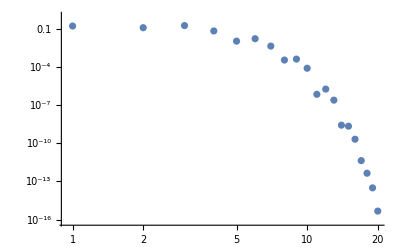

```mathematica
ListLogLogPlot[Table[Abs[f3hat[s ]]/. c -> 0/.x0-> 0 /.x2->0/.g-> 1  /. n-> 3,{s,1,20}]//N]
```

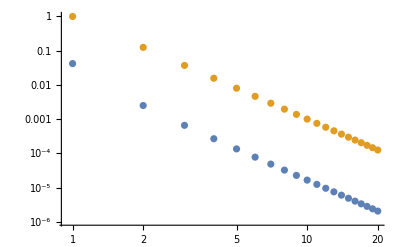

```mathematica
ListLogLogPlot[{Table[Abs[f2hat[s]]/.x0-> 0.5 /.x2->0.5/.g0-> 1/.g1->1 /.g2-> 1  /. n-> 3,{s,1,20}]//N,Table[1/s^3,{s,1,20}]}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating π^2\ (3699200\ ⅇ^60 + 2672672\ ⅇ^60\ π^2) + π^2\ (-3699200\ ⅇ^80 - 2672672\ ⅇ^80\ π^2) + Re[46240\ ⅇ^80\ (40 + 34\ ⅈ\ π)\ π^2\ Erf[40 + Times[« 2 »]/4\ √5] - 39304\ ⅈ\ ⅇ^80\ (40 + 34\ ⅈ\ π)\ π^3\ Erf[40 + Times[« 2 »]/4\ √5] - 924800\ ⅇ^80\ (2 - 17\ ⅈ\ π/10)\ π^2\ Erf[40 + Times[« 2 »]/4\ √5] - 786080\ ⅈ\ ⅇ^80\ (2 - 17\ ⅈ\ π/10)\ π^3\ Erf[40 + Times[« 2 »]/4\ √5]].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating π^2\ (4147200\ ⅇ^60 + 3359232\ ⅇ^60\ π^2) + π^2\ (-4147200\ ⅇ^80 - 3359232\ ⅇ^80\ π^2) + Re[51840\ ⅇ^80\ (40 + 36\ ⅈ\ π)\ π^2\ Erf[40 + Times[« 2 »]/4\ √5] - 46656\ ⅈ\ ⅇ^80\ (40 + 36\ ⅈ\ π)\ π^3\ Erf[40 + Times[« 2 »]/4\ √5] - 1036800\ ⅇ^80\ (2 - 9\ ⅈ\ π/5)\ π^2\ Erf[40 + Times[« 2 »]/4\ √5] - 933120\ ⅈ\ ⅇ^80\ (2 - 9\ ⅈ\ π/5)\ π^3\ Erf[40 + Times[« 2 »]/4\ √5]].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating π^2\ (4620800\ ⅇ^60 + 4170272\ ⅇ^60\ π^2) + π^2\ (-4620800\ ⅇ^80 - 4170272\ ⅇ^80\ π^2) + Re[57760\ ⅇ^80\ (40 + 38\ ⅈ\ π)\ π^2\ Erf[40 + Times[« 2 »]/4\ √5] - 54872\ ⅈ\ ⅇ^80\ (40 + 38\ ⅈ\ π)\ π^3\ Erf[40 + Times[« 2 »]/4\ √5] - 1155200\ ⅇ^80\ (2 - 19\ ⅈ\ π/10)\ π^2\ Erf[40 + Times[« 2 »]/4\ √5] - 1097440\ ⅈ\ ⅇ^80\ (2 - 19\ ⅈ\ π/10)\ π^3\ Erf[40 + Times[« 2 »]/4\ √5]].

General::stop: Further output of N :: meprec will be suppressed during this calculation.

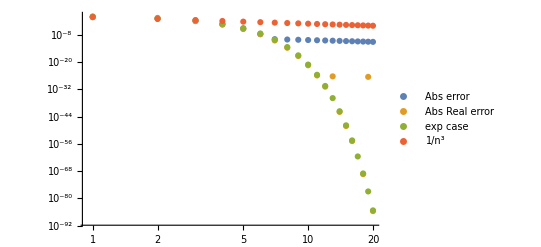

```mathematica
ListLogLogPlot[{
Table[Abs[f2hat[s ]]/.x0-> 0 /.x2->0/.g0-> 1/.g1->1/.g2-> 1  /. n-> 20,{s,1,20}]//N,
Table[Abs[Re[f2hat[s ]]]/.x0-> 0 /.x2->0/.g0-> 1/.g1->1/.g2-> 1  /. n-> 20,{s,1,20}]//N,
Table[Abs[f3hat[s ,0]]/.x0-> 0 /.x2->0/.g-> 1  /. n-> 20,{s,1,20}]//N,
Table[1/s^3,{s,1,20}]},PlotLegends ->{"Abs error","Abs Real error","exp case","1/n^3"}]
```

```mathematica
(* s rate is NOT quartic ITS CUBIC*)
```

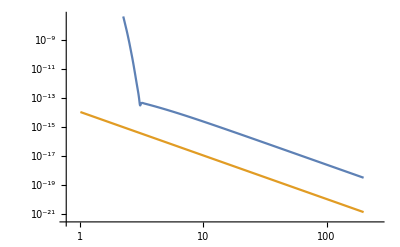

```mathematica
LogLogPlot[{Abs[f2hat[s]]/. n -> 3 /.g0->1/. g1-> 1/.g2 ->1 /.x0-> -2/.x2-> -2,10^-14/s^3 },{s,1,200}]
```

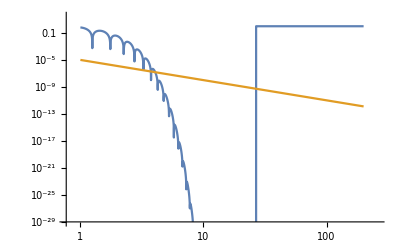

```mathematica
LogLogPlot[{N[Abs[Re[f3hat[s,0]]]]/. n -> 10 /.g->1 /.x0-> 0/.x2-> 0,10^-5/s^3 },{s,1,200}]
```

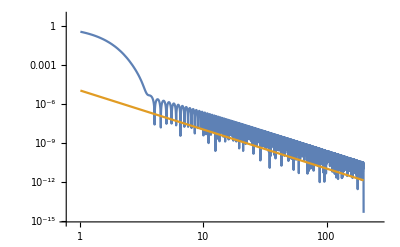

```mathematica
LogLogPlot[{N[Abs[Re[f2hat[s]]]]/. n -> 10 /.g0->1/. g1-> 1/.g2 ->1 /.x0-> 0/.x2-> 0,10^-5/s^3 },{s,1,200}]
```

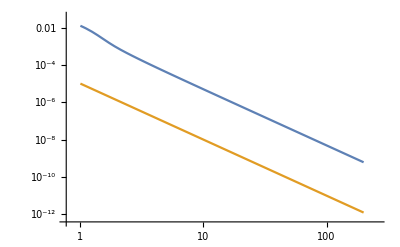

```mathematica
LogLogPlot[{Abs[f2hat[s]]/. n -> 3 /.g0->1/. g1-> 1/.g2 ->1 /.x0-> 0.8/.x2-> 0.8,10^-5/s^3 },{s,1,200}]
```

```mathematica
(* s rate is cubic???*)
```

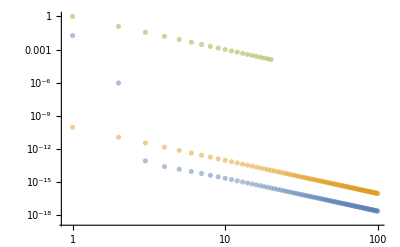

```mathematica
ListLogLogPlot[{
Table[Abs[f2hat[s ]]/.x0-> -2 /.x2->-2/.g0-> 1 /.g1->1/.g2-> 1  /. n-> 3,{s,1,100}]//N,
Table[Abs[vinv2[s ]]/.Kc -> 0/.x0-> -2 /.x2->-2/.g0-> 1 /.g2-> 1  /. n-> 3,{s,1,100}]//N,
Table[1/s^3,{s,1,20}]},
PlotStyle->{Opacity[0.5],Opacity[0.5],Opacity[0.5]}]
```

```mathematica
(*Should reduce to exponential case when we have linear boundaries*)
```

```mathematica
Manipulate[LogLogPlot[{
Abs[f2hat[s n^α]] /. g0 -> √(1 + 1-1/n)/. g1->√(1+1) /. g2-> √(1 + 1+1/n)/.x0-> x0s /.x2->x2s,
48 n n^(-4 α)/(30 (4!))(g2-x2)(g0-x0)PDF[NormalDistribution[0,1/(√n)],g1 - x2]PDF[NormalDistribution[0,1/(√n)],g1 - x0]/. g0 ->√(1 + 1-1/n)/. g1-> 1 /. g2->  √(1 + 1-1/n)/.x0-> x0s /.x2->x2s,
Abs[f3hat[s n^α,Kc]]/.x0-> x0s /.x2->x2s/.g->√(1+1) ,
Abs[vinv2[s n^α]]  /. g0 ->  √(1 + 1-1/n)/. g1->√(1+1) /. g2-> √(1 + 1-1/n)/.x0-> x0s /.x2->x2s,
1/n^4},
{n,1,10^3},PlotStyle->{Opacity[a],Opacity[b],Opacity[c],Opacity[d],Opacity[e]},PlotLegends ->{"Abs error","EMSF","exp case","Vincent v2","1/n^4"}],
{x0s,-3,1},
{x2s,-3,1},
{s,1,10,1},
{{Kc,0},-3,3},
{{α,1},0.5,1.5},
{{a,1,"ABS"},{1,0}},
{{b,1,"EMSF"},{1,0}},
{{c,1,"exp case"},{1,0}},
{{d,1,"vin"},{1,0}},
{{e,1,"1/n^4"},{1,0}},
ControlPlacement->Left]
```

```mathematica
(**)
```

```mathematica
Manipulate[LogLogPlot[{
Abs[f2hat[s n^α]] /. g0 -> √(1 +√((n-1)/n))/. g1->√(1+1) /. g2-> √(1 + √((n+1)/n))/.x0-> x0s /.x2->x2s,
Abs[f2hat[s n^α]] /. g0 -> (√2)/n(n-)/. g1->√2 t/. g2-> (√2)/n(n+1)/.x0-> x0s /.x2->x2s,
1/n^4},
{n,1,10^3},PlotStyle->{Opacity[a],Opacity[b],Opacity[c],Opacity[d],Opacity[e]},PlotLegends ->{"curve","linear","1/n^4"}, PlotLabel->"Does curvature matter?"],
{x0s,-3,1},
{x2s,-3,1},
{s,1,10,1},
{{Kc,0},-3,3},
{{α,1},0.5,1.5},
{{a,1,"ABS"},{1,0}},
{{b,1,"EMSF"},{1,0}},
{{c,1,"exp case"},{1,0}},
{{d,1,"vin"},{1,0}},
{{e,1,"1/n^4"},{1,0}},
ControlPlacement->Left]
```

```mathematica
Manipulate[LogLogPlot[{
Abs[f2hat[s n^α]]/Abs[vinv2[s n^α]] /. g0 -> 1-Kc/n/. g1-> 1 /. g2-> 1+Kc/n/.x0-> x0s /.x2->x2s,},
{n,1,10^3},PlotStyle->{Opacity[a]},PlotLegends ->{"Abs error"}],
{x0s,-3,1},
{x2s,-3,1},
{s,1,10,1},
{{Kc,0},-3,3},
{{α,1},0.5,1.5},
{{a,1,"ABS"},{1,0}},
ControlPlacement->Left]
```